# Positive Integer

### Author

Eric W. Weisstein
May 7, 2024

This notebook downloaded from http://mathworld.wolfram.com/notebooks/IntegerSequences/PositiveInteger.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/PositiveInteger.html.

©2024 Wolfram Research, Inc. except for portions noted otherwise

## Sequence

A000027

```mathematica
Table[n,{n,20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

## Recurrence Equation

```mathematica
RSolve[{a[n]==a[n-1]+1,a[1]==1},a[n],n]
```

{{a[n]→n}}

## Binary plot

```mathematica
BinaryPlot[f_,{n_,n0_,nmax_}]:=Module[{data=Table[IntegerDigits[Function[n,f][k],2],{k,n0,nmax}],len},
len=Max[Length/@data];
ArrayPlot[Transpose[PadLeft[#,len,0]&/@data],Frame->False]
]
```

```mathematica
GraphicsColumn[{BinaryPlot[n,{n,1,255}],BinaryPlot[n,{n,256,256+2 255}]},ImageSize->Large]
```

-Graphics-

## Plot

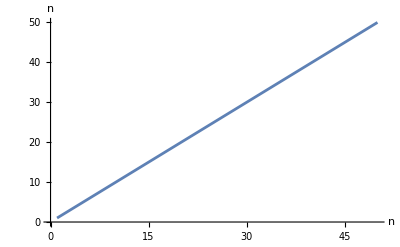

```mathematica
ListPlot[Range[50],AxesLabel->{n,n},Joined->True]
```

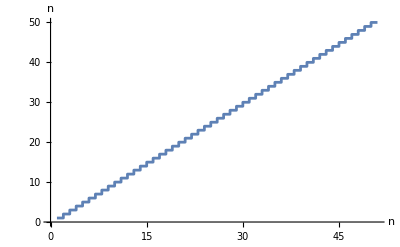

```mathematica
ListStepPlot[Range[50],AxesLabel->{n,n},Joined->True]
```

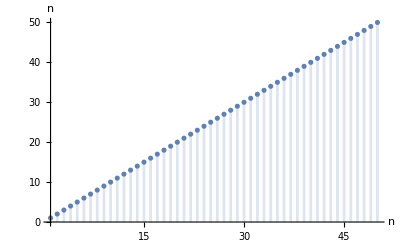

```mathematica
DiscretePlot[n,{n,50},AxesLabel->{n,n}]
```

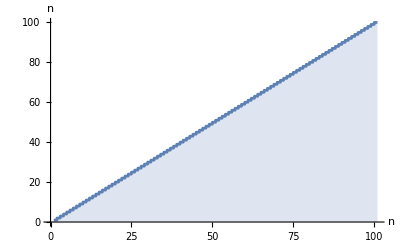

```mathematica
ListStepPlot[Range[100],Filling->Automatic,AxesLabel->{n,n},LabelStyle->Directive[Black,Opacity[1],FontFamily->"Times",12]]
```